```mathematica
$HistoryLength=3
```

3

## Daycount - Number of days in a month, given year and month

daycount[yyyy,mm] where yyyy and mm are numeric (strings or integers)

```mathematica
daycount[year_,month_]:=
Catch[
Module[{monthlengths},
If[Mod[year//ToExpression,4]==0,
monthlengths={31,29,31,30,31,30,31,31,30,31,30,31},
monthlengths={31,28,31,30,31,30,31,31,30,31,30,31}];
Throw[monthlengths[[month//ToExpression]]];
]];
```

## FindNearestNeighbor

Finds the members of “loc” that are nearest to the members of “findlist” according to smallest-square-distance. should work for 1, 2, 3, or higher dimension sets, only tested for x/y scatters

example:
s=OpenRead[“C:\\Users\\Sam\\Desktop\\station locations.txt”];
loc=ReadList[s,Number];
Close[s];
loc=Partition[loc,2];

findlist={{-77.422777777778,35.645277777778},
{-77.372777777778,35.616666666667},
{-77.175833333333,35.573888888889}};

```mathematica
FindNearestNeighbor[loc_,findlist_]:=
Catch[
Block[{neareststation,distancemin,distance},
neareststation=Table[0,{Length[findlist]}];
Do[
distancemin=9999999;
Do[
distance=Total[(loc[[station]]-findlist[[site]])^2];(* take square of distance between test pt (loc) and real location (findlist)*)
If[distance<distancemin,
distancemin=distance;
neareststation[[site]]=station;
];
,{station,1,Length[loc]}];
,{site,1,Length[findlist]}];
Throw[neareststation];
];
];
```

## Viewlist - show elements in a list using manipulate

Useful little “manipulate” call that brings up a window to view elements in some list. “i” is some free variable (block seems to give errors).

```mathematica
Viewlist[temp_,i_]:=Manipulate[temp[[i]],{i,1,Length[temp],1}]
```

## nashsutcliffe - NSE with no assumptions

```mathematica
(*-Graphics- Thanks, Wikipedia!*)
```

```mathematica
nashsutcliffe[qm_,qo_,times_]:=Module[{qobar,top,bottom},
qobar=Mean[qo[[1;;times]]];
top=Sum[(qo[[i]]-qm[[i]])^2,{i,1,times}];
bottom=Sum[(qo[[i]]-qobar)^2,{i,1,times}];
Return[1-(top/bottom)]
];
```

## ReadUSGSQfile - Reads a file in the common USGS station format, returns single column

fpath = filepath
headerrows = number of rows to skip
ncolumns = number of “word” columns - note that common date-time notation (mm/dd/yyyy hh:mm) is two “words” since Mathematica reads spaces as separators in ascii files

column of interest = number of column that has the data of interest
format = format of column (word, number, etc)

!! file must be “filled” i.e. each column/row combo needs data. Normal USGS gauge data format doesn’t put “NaN” values, they just leave blanks, so you’ll need to account for that !!

Also, since this is a good format for reading arbitrary ascii tables, it pops up in lots of other places in my code - sorry for the bad label D:

```mathematica
ReadUSGSQfile[fpath_,headerrows_,ncolumns_,columnofinterest_,format_]:=
Module[{s,table,L},
s=OpenRead[fpath];
table=ReadList[s,String];
Close[s];
L=Length[table];

table=Table[0,{L-headerrows}];
s=OpenRead[fpath];
Skip[s,String,headerrows];

Do[
Skip[s,Word,columnofinterest-1];
table[[i]]=Read[s,format];
Skip[s,Word,ncolumns-columnofinterest];
,{i,L-headerrows}];
Close[s];

Return[table]
];
```

## ReadUSGSQfileOld

reads old format (pre-2007) USGS file, looks for date information and data in the “columnofinterest”, and returns a scatter dataset of absolute times / data values

```mathematica
group[table_]:=
Table[StringJoin[table[[i]]]//ToExpression,{i,1,Length[table]}];

ReadUSGSQfileOld[fpath_,ncolumns_,datecolumn_,columnofinterest_,format_]:=
Catch[
Module[{s,raw,char,skip,yyyyMMddhhmmss,flows,yyyy,MM,dd,hh,mm,ss,times},
s=OpenRead[fpath];
raw=ReadList[s,String];
Close[s];
char=Characters[raw];

skip=Position[char,"#"];
skip=Length[skip]+2;

yyyyMMddhhmmss=ReadUSGSQfile[fpath,skip,ncolumns,datecolumn,Word];
flows=ReadUSGSQfile[fpath,skip,ncolumns,columnofinterest,format];

flows=Delete[flows,Position[yyyyMMddhhmmss,0]];
yyyyMMddhhmmss=Delete[yyyyMMddhhmmss,Position[yyyyMMddhhmmss,0]];
yyyyMMddhhmmss=Characters[yyyyMMddhhmmss];
yyyy=Transpose[yyyyMMddhhmmss][[1;;4]]//Transpose;
yyyy=group[yyyy];
MM=Transpose[yyyyMMddhhmmss][[5;;6]]//Transpose;
MM=group[MM];
dd=Transpose[yyyyMMddhhmmss][[7;;8]]//Transpose;
dd=group[dd];
hh=Transpose[yyyyMMddhhmmss][[9;;10]]//Transpose;
hh=group[hh];
mm=Transpose[yyyyMMddhhmmss][[11;;12]]//Transpose;
mm=group[mm];
ss=Transpose[yyyyMMddhhmmss][[13;;14]]//Transpose;
ss=group[ss];

times=Table[AbsoluteTime[{yyyy[[i]],MM[[i]],dd[[i]],hh[[i]],mm[[i]],ss[[i]]}],{i,1,Length[yyyy]}];
Throw[Transpose[Table[{times,flows}]]];
]];
```

## ReadRDHMQ - Calls “ReadUSGSQfile” to read an RDHM Q file. Caution: slow!

Inputs:
filepath = path of RDHM file

Outputs: Scatter in form {{t1,Q1},{t2,Q2}...{tn,Qn}}

At the moment, clocks in at 0.936s for a 9500 line file - this is slow! But I only need to run this a few times for my thesis (around 1000 times total, so runtime ~16 minutes) so it’s not worth refactoring (yet).

```mathematica
ReadRDHMQ[filepath_]:=
Catch[
Module[{s,raw,char,skip,flows,ddmmyy,dd,mm,yy,h,m,yyadjust,yyyy,times},
s=OpenRead[filepath];
raw=ReadList[s,String];
Close[s];
char=Characters[raw];

(*find lines that start with "$" and delete them from "raw" input*)
skip=Position[char,"$"];
skip=Length[skip];

(*two lines after the "$" lines, so skip those (second argument of ReadUSGSQfile)*)
(*Import data*)
flows=ReadUSGSQfile[filepath,skip+2,4,4,Number];
ddmmyy=ReadUSGSQfile[filepath,skip+2,4,2,Word];
(*when I do the read, I wind up with a bunch of "0" characters at the end of the file. Let's remove those...*)yy=Delete[ddmmyy,Position[ddmmyy,0]];
flows=Delete[flows,Position[ddmmyy,0]];
ddmmyy=Delete[ddmmyy,Position[ddmmyy,0]];
(*move them into a convenient format for "absoluteTime" function*)
dd=Transpose[Transpose[Characters[ddmmyy]][[1;;2]]];
dd=Table[StringJoin[dd[[i]]]//ToExpression,{i,1,Length[dd]}];
mm=Transpose[Transpose[Characters[ddmmyy]][[3;;4]]];
mm=Table[StringJoin[mm[[i]]]//ToExpression,{i,1,Length[mm]}];
yy=Transpose[Transpose[Characters[ddmmyy]][[5;;6]]];
yy=Table[StringJoin[yy[[i]]]//ToExpression,{i,1,Length[yy]}];
h=ReadUSGSQfile[filepath,skip+2,4,3,Number];
m=Table[0,{Length[h]}];
s=m;
(*years are in "yy" format - absolute time needs the millenium*)
yyadjust=Table[0,{Length[yy]}];
Do[
(*code written in 2015 for storms no older than 1990 - any yy < 20 is 20yy, any yy >20 is 19yy*)
If[yy[[i]]<20,
yyadjust[[i]]=2000,
yyadjust[[i]]=1900];
,{i,1,Length[yy]}];
yyyy=yy+yyadjust;


times=Table[AbsoluteTime[{yyyy[[i]],mm[[i]],dd[[i]],h[[i]],m[[i]],s[[i]]}],{i,1,Length[flows]}];
Throw[Transpose[Table[{times,flows}]]];
]]
```

## asciiFileSubset - looks for info in a messy ascii file, exports to a target

Reads lines in a text file, looking for “preline.” if it finds “preline” it then begins writing subsequent lines to an output file, until it reads “postline.” Repeats until file end. If “delimit” = TRUE, inserts “delimiter” line in between each read section. Example inputs in comments.

```mathematica
(*
fpath="D:\\Dropbox\\HEC-RAS\\HEC-RAS Mainstem Only\\HEC-RAS Mainstem Only\\Mainstem.RASexport.sdf";
fpathOut="D:\\Dropbox\\HEC-RAS\\HEC-RAS Mainstem Only\\cutlines.txt";
preline="    CUT LINE:";
postline="    SURFACE LINE:";
delimit=True;
delimiter="xsection"
*)
```

```mathematica
asciiFileSubset[fpath_,fpathOut_,preline_,postline_,delimit_,delimiter_]:=
Block[{s,l,so,infoflag,test,data},


s=OpenRead[fpath];
temp=ReadList[s,String];
l=Length[temp];
Close[s];
Clear[temp];

(*Viewlist[temp,i] <- Use this cell after initial read to define preline, postline*)
s=OpenRead[fpath];
so=OpenWrite[fpathOut];
infoflag=0;
Do[
If[infoflag==0,
test=Read[s,String];
If[test==preline,
infoflag=1;
];
];

If[infoflag==1,
data=Read[s,String];
If[data==postline,
infoflag=0;
If[delimit==True,
Write[so,delimiter];
];
,Write[so,data];
];
];
,{l}];


Close[s];
Close[so];
]
```

## scatterNSinterp - interpolates model scatter, then calculates NSE

Irregular Data NSE (average and compare)
generate (using some other script) two scatters to be compared, with format {{t1,y1},{t2,y2}...,{tn,yn}} where tx is the xth time measurement and yx is the xth quantity measured (flow, stage, etc) 

The output is {nse,gaplossobs,gaplossmod,overlap,obqs,modqs}. 

“Gap” means some data did not overlap and was excluded. “obs” vs “mod” tells you if the lost data came from observed or model dataset. IE Gaplossmod is harmless, gaplossobs is bad.  Overlap is the average number of extra data entries averaged into each averaging bin. IE if you have 5 minute data and want the NSE over 15 minute intervals, overlap will be two (three 5-minute data points per 15-minute “bin”, so two “overlapped” data points). Ideally gaplossobs, gaplossmod, and overlap will all be zero. The real best answer for “increment” minimizes the three, and the best averaged NSE will take sensitivity to “increment” into account. 

obqs and modqs are just the averaged timeseries for each parameter. It’d be good practice to plot these along with the original data to make sure they are representing the behavior of the system.

```mathematica
(*method can take values of "Hermite" or "Spline". Best practice will test both.*)

scatterNSinterp[obscatter_,modelscatter_,method_]:=

(*set timeinc to the length of "bins" to be used*)

Catch[
Module[{obtimes,interp,modqs,obqs,obqm,topsumsq,botsumsq,nse},
(*step 1: find the list of times for which we have observations*)
obtimes=Transpose[obscatter][[1]];

(*step 2: define an interpolating function*)
interp=Interpolation[modelscatter,Method->method];

(*step 3: call function for all values of times*)
modqs=interp[obtimes];
obqs=Transpose[obscatter][[2]];

(*calculate NSE*)
-Graphics-;
;
obqm=Mean[obqs];
topsumsq=Sum[(obqs[[i]]-modqs[[i]])^2,{i,1,Length[obqs]}];
botsumsq=Sum[(obqs[[i]]-obqm)^2,{i,1,Length[obqs]}];
nse=1-(topsumsq)/(botsumsq);
Throw[{nse,Transpose[Table[{obtimes,obqs}]],Transpose[Table[{obtimes,modqs}]]}];
]];
```

Hermite

original datasets:

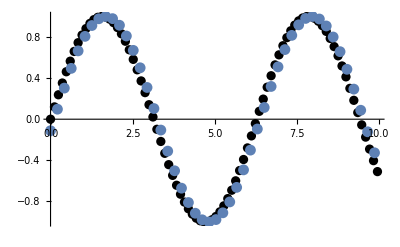

InterpolatingFunction::dmval: Input value {9.96} lies outside the range of data in the interpolating function. Extrapolation will be used.

NSE: 0.984906

model data vs. representation after averaging:

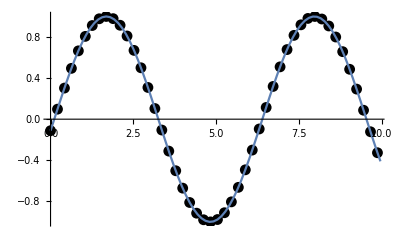

observed data vs. interpolated model values

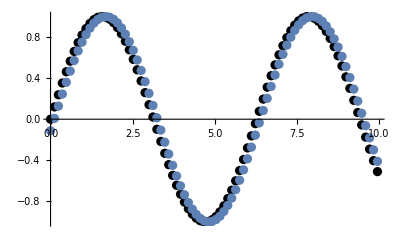

```mathematica
(*this is a simple example, showing how the function works and a few good "due diligence" steps. Try varying increment to see how the model fit changes*)
obset=Table[{x,Sin[x]},{x,0,10,0.12}];
modset = Table[{y,Cos[y+4.6]},{y,0,10,0.21}];
method="Hermite"

"original datasets:"
Show[ListPlot[obset,PlotStyle->Black],ListPlot[modset]]
result=scatterNSinterp[obset,modset,method];

StringJoin["NSE: ",ToString[result[[1]]]]




"model data vs. representation after averaging:"
Show[ListPlot[modset,PlotStyle->Black],ListPlot[result[[3]],Joined->True]]

"observed data vs. interpolated model values"
Show[ListPlot[obset,PlotStyle->Black],ListPlot[result[[3]]]]

(*using this example, Hermite gives NSE of "NSE: 0.984906"*)
(*Spline gives NSE of "NSE: 0.984906"*)
```

## NSEtable - tabulates NSE using many lists of model scatters. Calls scatterNSinterp

Calls “scatterNS”, creates a table of the results. Useful for finding the “best” member among multi-member ensembles.

```mathematica
NSEtable[modelScatters_,obscatter_,method_]:=
Block[{temp,nmembers,i},
nmembers=Length[modelScatters];
temp=Table[0,{nmembers}];

Do[
temp[[i]]=scatterNSinterp[obscatter,modelScatters[[i]],method];
,{i,1,nmembers}];

Return[temp];
];
```

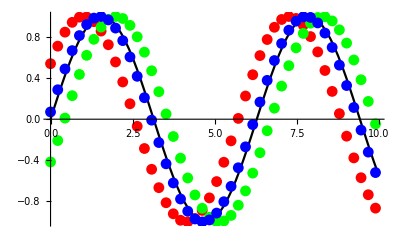

{0.630826,0.781971,0.994038}

{{3}}

```mathematica
observedScatter=Table[{x,Sin[x]},{x,0,10,0.12}];
modelScatters={
Table[{x,Cos[x-1]},{x,0,10,0.22}],(*"red"*)
Table[{x,Cos[x-2]},{x,0,10,0.22}], (*"green"*)
Table[{x,Cos[x-1.5]},{x,0,10,0.22}] (*"blue"*)
};

Show[ListPlot[observedScatter,Joined->True,PlotStyle->Black],ListPlot[modelScatters[[1]],PlotStyle->Red],ListPlot[modelScatters[[2]],PlotStyle->Green],ListPlot[modelScatters[[3]],PlotStyle->Blue]]

NSElist=NSEtable[modelScatters,observedScatter,"Spline"];
NSEs=Transpose[NSElist][[1]]
BestMember=Position[NSEs,Max[NSEs]]
```

## stationsAnd61Import - imports station locations and fort.61 WSE timeseries

This function is a little esoteric. It’s purpose is to import the locations (fort.15) and WSE timeseries information (Fort.61) for a set of ADCIRC stations in one or more cross-sections of interest (xsecs), then export that information to a set of ascii files. It’s basically a data trimming operation, meant to shrink the (potentially quite large) fort.61 files into a more manageable dataset. 

INPUTS
fpath15 - fort.15 file used in the run
start - line in fort.15 file of the first station’s location
end - line in fort.15 file of the last station’s location
xsecstart/xsecend - in the set of stations, the number of the station that is the beginning of the xsection of 	interest. i.e. if you have 100 stations total and you want info for the 5th through the 17th station, 		xsecstart is 5, xsecend is 17. 
bathypath - filepath of station bathymetry info
	(default bathypath=”C:\\Users\\Sam\\Desktop\\Thesis Work\\ADCIRC\\Data reading - 			bathymetries\\stationBathy.txt”;(*text file. one column. one value for each station*)
path61 - some fort.61
wseoutpath - output path for all WSE data at the stations. That means for a section with 10 stations, 		there’ll be 10 timeseries. useful for debugging
avgWSEoutpath - timeseries of average WSE across the river xsection. that means for a section with 10 		stations, there’s only one timeseries. This is what will be reported generally.
headerinfo - extra info that gets tacked on to the “throw” list. Useful for debugging. 

OUTPUTS
headerinfo - as above, verbatim
lastx - list of easting coordinates (feet) according to the projection given. Note: you must manually change grid parameters for this to be accurate!!!!!
lasty - as lastx, but northing coordinates 
lastz - elevation of stations in xsection
WSEtimeseries - average WSE timeseries for the x-section, excluding dry areas. 

NOTE TO SELF - when you have some time, refactor this to instead just take the lines of fort.15 indicating the stations of interest

```mathematica
stationsAnd61Import[fpath15_,start_,end_,xsecstart_,xsecend_,bathypath_,path61_,wseoutpath_,avgWSEoutpath_,headerinfo_]:=
Catch[
Module[{nstations,stationlat,stationlon,s15,slam0,sfea0,NAN,d2r,R,slam0r,sfea0r,slam,stationx,sfea,stationy,lastx,lasty,bathystream,
stationbathys,lastz,dist,s,temp,L,totalstations,timesteps,xsecstations,ts,validateTable,WSEtimeseries,deletelist,NaN,},
nstations=end-start+1;
(*
n61header=908;
n61headerstations=start-n61header;
n62header=;
n62stationstart=;
n62header=;
*)
(*
"i"
Dynamic[i]
"j"
Dynamic[j]
StringJoin["validation Table - should be list of station indexes, going from ",ToString[xsecstart]," (xsecstart) to ",ToString[xsecend]," (xsecend)"]
Dynamic[validateTable]
*)


stationlat=Table[0,{nstations}];
stationlon=Table[0,{nstations}];

s15=OpenRead[fpath15];
Skip[s15,String,(start-1)];

Do[
stationlon[[i]]=Read[s15,Number];
stationlat[[i]]=Read[s15,Number];
Skip[s15,String];
,{i,1,nstations}];

Close[s15];

(* convert lat/longs into x/y *)
slam0=-79.0;(*center longitude*)
sfea0=35.0;(*center latitude*)
NAN="NAN";(*Designator for non-values*)

d2r=3.14159265358979323/180;
R=6378206.4;
slam0r=slam0*d2r;
sfea0r=sfea0*d2r;

slam=stationlon*d2r;
stationx=R*(slam-slam0r)*Cos[sfea0r];
sfea=stationlat*d2r;
stationy=R*sfea;
(*irene: last ds bc is at positions 192-596*)
lastx=stationx[[xsecstart;;xsecend]];
lasty=stationy[[xsecstart;;xsecend]];

(*import station bathymetries*)
bathystream=OpenRead[bathypath];
stationbathys=ReadList[bathystream];
lastz=stationbathys[[xsecstart;;xsecend]];
Close[bathystream];


(*visualize river x-section, if applicable*)
dist=Table[((lastx[[i]]-Min[lastx])^2+(lasty[[i]]-Min[lasty])^2),{i,1,Length[lastx],1}];

(*Generate WSE timeseries at each station's points*)
s=OpenRead[path61];
temp=ReadList[s,String];
L=Length[temp];
Close[s];

(*import 61 timeseries for target x-section*)
totalstations=nstations;
timesteps=(L-2)/(totalstations+1);

xsecstations=xsecend-xsecstart+1;

ts=Table[Table[0,{timesteps}],{xsecstations}];	
validateTable=Table[0,{xsecstations}];

s=OpenRead[path61];
Skip[s,String,xsecstart+2];(* *)

Do[
Do[
validateTable[[i]]=Read[s,Number];
ts[[i,j]]=Read[s,Number];
,{i,1,xsecstations}];
Skip[s,String,totalstations+1-xsecstations];(*<-- Replace with the total number of stations - the number of stations before the target xsection *)
,{j,timesteps}];
Close[s];

Export[wseoutpath,ts];


(*this section calculates the average WSE at each timestep*)
WSEtimeseries=Transpose[ts];

Do[
	deletelist={};
	Do[
		If[WSEtimeseries[[i,j]]<-999,
			deletelist=Append[deletelist,{j}];
		]
	,{j,1,Length[WSEtimeseries[[i]]]}];
	WSEtimeseries[[i]]=Delete[WSEtimeseries[[i]],deletelist];
,{i,1,Length[WSEtimeseries]}];

Do[
	If[WSEtimeseries[[i]]=={},
		WSEtimeseries[[i]]=NaN;,
		WSEtimeseries[[i]]=Median[WSEtimeseries[[i]]];
	];
,{i,1,Length[WSEtimeseries]}];

Export[avgWSEoutpath,WSEtimeseries];
"median WSE timeseries at DS boundary"

Throw[{headerinfo,lastx,lasty,lastz,WSEtimeseries}];
](*end module*)
];

(*relevant stored variables: 

WSEtimeseries
ts
stationBathys*)
```

## anglesAndMagsClockwiseFromNorth - Takes u,v data and converts to magnitude/angle

```mathematica
(*angle between v1 and v2 = arccos[ Dot[v1,v2] / Abs[v1]*Abs[v2]], with sign of det. 
determining if the angle is clockwise (+) or counter-clockwise(-)*)

(*method 1 - ARcCos[dot]
NOT CURRENTLY FUNCTIONAL!!!!
*)

(*
windstrength=(uxs^2+vys^2)^(1/2);
windvectors=Table[{uxs[[i,j]],vys[[i,j]]},{i,1,nstations},{j,1,l}];
windDotOrigin=Table[Dot[windvectors[[i,j]],originVector],{i,1,nstations},{j,1,l}];
windDetOrigin=Table[Det[{windvectors[[i,j]],originVector}],{i,1,nstations},{j,1,l}];
internalAngle=Table[ArcCos[windDotOrigin[[i,j]]/windstrength[[i,j]]],{i,1,nstations},{j,1,l}];
clockwiseAngle=Table[0,{i,1,nstations},{j,1,l}];
Do[
Do[
If[windDetOrigin[[i,j]]<0,
clockwiseAngle[[i,j]]=2*Pi-internalAngle[[i,j]];
,clockwiseAngle[[i,j]]=internalAngle[[i,j]];
];
,{i,1,nstations}];
,{j,1,l}];


clockwiseAngleRad=clockwiseAngle;
clockwiseAngleDeg=clockwiseAngle*180/Pi;
*)

(*
method 2 - 
w is wind vector
n is northing vector (0,1)
cos(theta) = w.n/|w|*|n|
theta = arccos w.n / |w|*|n|
then apply special cases - if easting is positive, angle is theta.
If easting is negative, angle is 360 - theta.
If easting is zero and northing is zero or positive, angle is zero
if easting is zero and northing is negative, angle is 180. 

Otherwise determine the quadrant and calculate the resulting thetas.
*)
anglesAndMagsClockwiseFromNorth[us_,vs_]:=
Catch[
Module[{origin,L,vectors,dots,mags,angles,base},
origin={0,1};
If[Length[us]!=Length[vs],Throw["Error! us and vs need to be the same length."]];
L=Length[us];
vectors=Table[{us[[i]],vs[[i]]},{i,1,L}];
dots=Table[vectors[[i]].origin,{i,1,L}];
mags=Table[Sqrt[(us[[i]]^2+vs[[i]]^2)],{i,1,L}];
angles=Table[0,{L}];

Do[
If[us[[i]]==0&&vs[[i]]≥0,angles[[i]]=0];
If[us[[i]]==0&&vs[[i]]<0,angles[[i]]=180];
If[us[[i]]>0&&vs[[i]]==0,angles[[i]]=90];
If[us[[i]]<0&&vs[[i]]==0,angles[[i]]=270];
If[mags[[i]]>0,
base=ArcCos[dots[[i]]/mags[[i]]]*180/Pi;
];
If[us[[i]]>0&&vs[[i]]>0,angles[[i]]=base];
If[us[[i]]>0&&vs[[i]]<0,angles[[i]]=base];
If[us[[i]]<0&&vs[[i]]<0,angles[[i]]=360-base];
If[us[[i]]<0&&vs[[i]]>0,angles[[i]]=360-base];
,{i,1,L}];

Throw[{angles,mags}]
]
];
```

## ts72 - reads fort.72 (wind velocity at stations)

```mathematica
ts72[fpath_]:=
(
Module[{s,temp,filelength,nstations,ntimes,timestamps,vs,uxs,vys},
s=OpenRead[fpath];
temp=ReadList[s,String];
filelength=Length[temp];
Close[s];

s=OpenRead[fpath];
Read[s,String]; (*Line 1*)
Read[s,Word];
nstations=Read[s,Number];

ntimes=(filelength-2)/(nstations+1);
timestamps=Table[0,{ntimes}];
uxs=Table[0,{ntimes}];
vys=uxs;
vs=vys;

Read[s,String]; (*Line 2*)


Do[
timestamps[[i]]=Read[s,Number]; 
Read[s,String];
vs[[i]]=ReadList[s,Number,3*nstations]; 
vs[[i]]=Partition[vs[[i]],3];
uxs[[i]]=Transpose[vs[[i]]][[2]];
vys[[i]]=Transpose[vs[[i]]][[3]];
,{i,1,ntimes}];

Close[s];

Return[{Transpose[uxs],Transpose[vys],nstations,timestamps,ntimes}];
]);
```

## ReadNBDCfile - reads NBDC weather station file, returns single column

```mathematica
ReadNBDCfile[fpath_,headerrows_,ncolumns_,columnofinterest_,format_]:=
Module[{s,table,L},
s=OpenRead[fpath];
table=ReadList[s,String];
Close[s];
L=Length[table];

table=Table[0,{L-headerrows}];
s=OpenRead[fpath];
Skip[s,String,headerrows];

Do[
Skip[s,Word,columnofinterest-1];
table[[i]]=Read[s,format];
Skip[s,Word,ncolumns-columnofinterest];
,{i,L-headerrows}];
Close[s];

Return[table]
];
```

## OBSOLETE - scatterNSmean - sorts data into common bins, averages the bins and applies NSE

generate (using some other script) two scatters to be compared, with format {{t1,y1},{t2,y2}...,{tn,yn}} where tx is the xth time measurement and yx is the xth quantity measured (flow, stage, etc) 

The output is {nse,gaplossobs,gaplossmod,overlap,obqs,modqs}. 

“Gap” means some data did not overlap and was excluded. “obs” vs “mod” tells you if the lost data came from observed or model dataset. IE Gaplossmod is harmless, gaplossobs is bad.  Overlap is the average number of extra data entries averaged into each averaging bin. IE if you have 5 minute data and want the NSE over 15 minute intervals, overlap will be two (three 5-minute data points per 15-minute “bin”, so two “overlapped” data points). Ideally gaplossobs, gaplossmod, and overlap will all be zero. The real best answer for “increment” minimizes the three, and the best averaged NSE will take sensitivity to “increment” into account. 

obqs and modqs are just the averaged timeseries for each parameter. It’d be good practice to plot these along with the original data to make sure they are representing the behavior of the system.

```mathematica
scatterNSmean[obscatter_,modelscatter_,timeinc_]:=

(*set timeinc to the length of "bins" to be used*)
Catch[
Module[{L,times1,vals1,times2,vals2,commonstart,commonend,bin,binstart,binstop,obqs,modqs,gaps,obqm,topsumsq,botsumsq,nse,overlaplist,overlap, gapnum,gaplossmod,gaplossobs},




(*let's say we want to do an N-S calculation on a 15-minute time interval.*)
(*step 1 is to calculate the extent of each scatter*)
times1=Transpose[obscatter][[1]];
vals1=Transpose[obscatter][[2]];
times2=Transpose[modelscatter][[1]];
vals2=Transpose[modelscatter][[2]];
commonstart=Max[Min[times1],Min[times2]];
commonend=Min[Max[times1],Max[times2]];

(*step 2 is to find out how many 15-minute intervals there are, shared among the two scatters.*)
(*e.g. let's say the two timeseries' start at 0:00 and 15:00, commonstart would be 15:00*)
(*then if commonend is 20:00, L is 5 hours, divided by 15 minutes gives L = 20 bins.*)
L=(commonend-commonstart)/timeinc;
L=Ceiling[L];
(*bin is a table of the observations or forecasts in each 15-minute interval*)
bin=Table[{{},{}},{L}];

(*for each bin, calculate the time extents*)
Do[
binstart=commonstart+(i-1)*timeinc;
binstop=commonstart+i*timeinc;

(*collect obscatter's entries that fit the bin*)
Do[
If[times1[[j]]<binstop,
If[times1[[j]]≥binstart,
bin[[i,1]]=Flatten[Append[bin[[i,1]],vals1[[j]]]];
];
];
,{j,1,Length[obscatter]}];

(*collect modelscatter's entries that fit the bin*)
Do[
If[times2[[j]]<binstop,
If[times2[[j]]≥binstart,
bin[[i,2]]=Flatten[Append[bin[[i,2]],vals2[[j]]]];
];
];
,{j,1,Length[modelscatter]}];

,{i,1,L}];
(*now measure each series' overlap, i.e. the sum of the avg. number of entries in each bin -1 *)
overlaplist=Table[If[Length[bin[[i,1]]]+Length[bin[[i,2]]]-2>0,Length[bin[[i,1]]]+Length[bin[[i,2]]]-2,0],{i,1,Length[bin]}];
overlap=Mean[overlaplist];

Do[
Transpose[gaps][[1]]

,{i,1,Length[gaps]}];

(*now replace all (extant) bins with the mean of the contents of that bin*)
Do[
Do[
If[bin[[i,j]]≠{},
bin[[i,j]]=Mean[bin[[i,j]]];
];
,{j,1,2}];
,{i,1,Length[bin]}];

(*now that all bins are populated & averaged, delete gaps*)
(*while doing so, track the number of actual values that are deleted*)

obqs=Transpose[bin][[1]];
modqs=Transpose[bin][[2]];
gapnum=0;
(*remove gaps - pass 1*)
gaps=Position[obqs,{}];
gaplossmod=Sum[Length[modqs[[gaps[[i]]]]],{i,1,Length[gaps]}];
obqs=Delete[obqs,gaps];
modqs=Delete[modqs,gaps];

(*remove gaps - pass 2*)
gaps=Position[modqs,{}];
gaplossobs=Sum[Length[obqs[[gaps[[i]]]]],{i,1,Length[gaps]}];
obqs=Delete[obqs,gaps];
modqs=Delete[modqs,gaps];

(*calculate NSE*)
-Graphics-;
obqs=Flatten[obqs];
modqs=Flatten[modqs];
obqm=Mean[obqs];
topsumsq=Sum[(obqs[[i]]-modqs[[i]])^2,{i,1,Length[obqs]}];
botsumsq=Sum[(obqs[[i]]-obqm)^2,{i,1,Length[obqs]}];
nse=1-(topsumsq)/(botsumsq);
Throw[{nse,gaplossobs,gaplossmod,overlap,obqs,modqs}];
]];
```

original datasets:

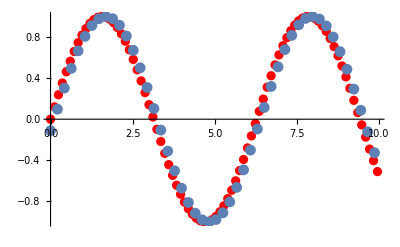

NSE: 0.951418

gaploss in observed: 0

gaploss in modeled: 0

overlap: 0.765957

observed data vs. representation after averaging:

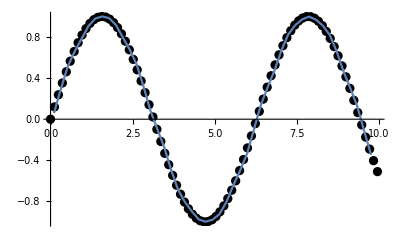

model data vs. representation after averaging:

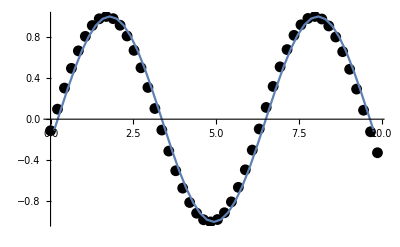

```mathematica
(*this is a simple example, showing how the function works and a few good "due diligence" steps. Try varying increment to see how the model fit changes*)
obset=Table[{x,Sin[x]},{x,0,10,0.12}];
modset = Table[{y,Cos[y+4.6]},{y,0,10,0.21}];
increment=0.21;
"original datasets:"
Show[ListPlot[obset,PlotStyle->Red],ListPlot[modset]]
result=scatterNSmean[obset,modset,increment];

StringJoin["NSE: ",ToString[result[[1]]]]
StringJoin["gaploss in observed: ",ToString[result[[2]]]]
StringJoin["gaploss in modeled: ",ToString[result[[3]]]]
StringJoin["overlap: ",ToString[N[result[[4]]]]]

"observed data vs. representation after averaging:"
Show[ListPlot[obset,PlotStyle->Black],ListPlot[Table[{(i-1)*increment+increment/2,result[[5,i]]},{i,1,Length[result[[5]]]}],Joined->True]]

"model data vs. representation after averaging:"
Show[ListPlot[modset,PlotStyle->Black],ListPlot[Table[{(i-1)*increment+increment/2,result[[6,i]]},{i,1,Length[result[[6]]]}],Joined->True]]
```

## Import NOS data

This function queries the NOS website for tidal station information, then turn that information into an x/y scatter dataset where X is the absolute time and Y is the tidal elevation at that station.
The basic one is NOSimportmonth, which grabs a maximum of 31 days’ data. 

Inputs include
stationnum - “nnnnnnnn” (Full NOS station number (7 digits)) as string or int)
startdate - “YYYYMMDD” (8 digit number, as string or integer)
enddate - “YYYYMMDD” (8 digit number, as string or integer)

```mathematica
NOSimportmonth[stationnum_,startdate_,enddate_]:=
Catch[
Block[{impath,imp,xy,times,vals},

impath=StringJoin["http://tidesandcurrents.noaa.gov/api/datagetter?product=water_level&application=NOS.COOPS.TAC.WL&begin_date=",ToString[startdate],"&end_date=",ToString[enddate],"&datum=MSL&station=",ToString[stationnum],"&time_zone=GMT&units=metric&interval=&format=csv"];
imp=Import[impath];
If[Length[imp]==0,
Throw[{}],
imp=imp[[2;;Length[imp]]];(*strip header*)
imp=Transpose[imp]; (*1 date column, 1 data column*)

times=Table[AbsoluteTime[imp[[1,i]]],{i,1,Length[imp[[1]]]}]; (*create time column from date column*)
vals=Table[imp[[2,i]],{i,1,Length[imp[[2]]]}]; (*create value column*)

xy=Transpose[Table[{times,vals}]]; (*make time/value scatter*)
Throw[xy];
];
];
];
```

This next, more useful function, generalizes the process by breaking any range into 31-day bites and importing their information, then concatenating the data into a single set. Be warned - this many calls to download data can take a while. It requires NOSimportmonth[] and daycount[] functions, as defined above

```mathematica
NOSimportrange[stationnum_,startyear_,startmonth_,startdate_,endyear_,endmonth_,enddate_]:=
Catch[
Block[{monthstrings,daystrings,completeyears,completemonths1,completemonths2,incompletemonths,incompleteyears,tstable},
(* Example Inputs*)
(*
startyear=2012;
startmonth=5;
startdate=17;

endyear=2016;
endmonth=10;
enddate=17;
stationnum=8410140;
*)
(*example inputs 2 - floyd*)
(*
stationnum=8410140;
startyear=1999;
startmonth=8;
startdate=11;
endyear=1999;
endmonth=10;
enddate=16;
*)

monthstrings=Table[ToString[i],{i,1,12}];
daystrings=Table[ToString[i],{i,1,31}];

(*this is a cheesy way of ensuring that "1" becomes "01" while "10" stays "10" for months and days*)
Do[
monthstrings[[i]]=StringJoin["0",monthstrings[[i]]];
daystrings[[i]]=StringJoin["0",daystrings[[i]]];
,{i,1,9}];


(*startdate="20130917";
enddate="20140917";*)

(*step 1 - break target interval into 31 day sections (NOS website only allows queries of length 31 days or less*)

(*Plan - 
1. figure out if any complete years need to be collected
2. figure out if any complete months in incomplete years need to be collected
3. collect incomplete months "im"
4. collect complete months "cm"
5. collect complete years "cy"
*)

(*1*)
If[endyear-startyear>1,
completeyears=Table[startyear+i,{i,1,endyear-startyear-1}]];
incompleteyears=Union[{startyear,endyear}];

(*2*)
If[Length[incompleteyears]==1, (*there's one incomplete year, meaning incomplete months run from startmonth to endmonth*)
completemonths1=Table[i,{i,startmonth+1,endmonth-1}],
completemonths1=Table[i,{i,startmonth+1,12}];
completemonths2=Table[i,{i,1,endmonth-1}]
];


(*3*)
incompletemonths=Union[{startmonth,endmonth}];

(*order - incompletemonth1, completemonths1, completeyears, completemonths2, incompletemonth2*)

(*allocate space for each*)
tstable=Table[0,{i,1,(Length[incompletemonths]+Length[completemonths1]+12*Length[completeyears]+Length[completemonths2])}];

(*get first incomplete month*)
tstable[[1]]=NOSimportmonth[stationnum,
	StringJoin[
		ToString[startyear],
		monthstrings[[startmonth]],
		daystrings[[startdate]]]
	,
	StringJoin[
		ToString[startyear],
		monthstrings[[startmonth]],
		daystrings[[daycount[startyear,startmonth]]]]
	];(*incomplete month 1*)

(*get first string of complete months in the first incomplete year*)
Do[
	tstable[[1+i]]=NOSimportmonth[stationnum,
		StringJoin[ToString[startyear],monthstrings[[completemonths1[[i]]]],"01"],
		StringJoin[ToString[startyear],monthstrings[[completemonths1[[i]]]],ToString[daycount[startyear,completemonths1[[i]]]]]
	];
,{i,1,Length[completemonths1]}]                    (*complete months 1, start day *)

(*get all the complete years*)
Do[
	Do[
		tstable[[1+Length[completemonths1]+12*(i-1)+j]]=NOSimportmonth[stationnum,
		StringJoin[ToString[completeyears[[i]]],monthstrings[[j]],"01"],
		StringJoin[ToString[completeyears[[i]]],monthstrings[[j]],ToString[daycount[completeyears[[i]],j]]]
	]
,{j,1,12}];
,{i,1,Length[completeyears]}];

(*get the complete months in the second incomplete year, if it exists*)
Do[
	tstable[[1+Length[completemonths1]+12*Length[completeyears]+i]]=NOSimportmonth[stationnum,
		StringJoin[ToString[endyear],monthstrings[[completemonths2[[i]]]],"01"],
		StringJoin[ToString[endyear],monthstrings[[completemonths2[[i]]]],ToString[daycount[startyear,completemonths2[[i]]]]]
	];
,{i,1,Length[completemonths2]}];    

(*get the second incomplete month (the end month) *)
tstable[[Length[tstable]]]=NOSimportmonth[stationnum,
	StringJoin[
		ToString[endyear],
		monthstrings[[endmonth]],
		"01"]
	,
	StringJoin[
		ToString[endyear],
		monthstrings[[endmonth]],
		daystrings[[enddate]]]
	];(*incomplete month 1*)  

(*Concatenate them all*)
tstable=Partition[Flatten[tstable],2];
If[Length[tstable]<2,tstable={{0,-999}}];
Throw[tstable]
](*end block*)
](*end catch*)
```

## axisdate

Simple function to provide axis labels every “lines” days - e.g. 7 is weekly - starts axis labels 1/2 week after xmin.
xmin,xmax - absolute time (in seconds)

```mathematica
axisdate[xmin_,xmax_,lines_]:=Table[{time+60*60*12*lines,DateString[time+60*60*12*lines,{"MonthShort","/","DayShort"}]},{time,xmin,xmax,(60*60*24*lines)}];
```

## scatterplot

My default plot for a {time, value} scatter dataset

```mathematica
scatterplot[scatter_,xstart_,xend_,ystart_,yend_,ylab_,xlab_,title_,daylines_,joined_,color_]:=
ListPlot[scatter,
Joined->joined,
PlotRange->{{xstart,xend},{ystart,yend}},
Frame->True,
FrameTicks->{{Automatic,None},
{axisdate[xstart,xend,daylines],None}},
FrameLabel->{{ylab,None},{xlab,title}},
GridLines->{Table[time+60*60*12*daylines,{time,xstart,xend,60*60*24*daylines}],Automatic},
BaseStyle->{FontSize->14,FontFamily->"Times New Roman"},
ImageSize->Large,
PlotStyle->color
]
```

## ReadMax

reads maxele file
returns list of nodal maxeles and times of occurrence

```mathematica
ReadMaxAll[fpath_]:=
Catch[
Module[{s,junk,np,maxel,maxeltime},
s=OpenRead[fpath];
junk=Read[s,String];
junk=Read[s,Number];

np=Read[s,Number];
maxel=Table["NAN",{np}];
maxeltime=maxel;

junk=Read[s,String];
junk=Read[s,String];

Do[
junk=Read[s,Number];
maxel[[i]]=Read[s,Number];
,{i,1,np}];

Do[
junk=Read[s,Number];
maxeltime[[i]]=Read[s,Number];
,{i,1,np}];

Throw[{maxel,maxeltime}];
];
];
```

## Plot adcirc data vs. observed

storm = {irene}
station = {rock_springs,grimesland,greenville}

```mathematica
(*hurricane irene*)

plotgauge[storm_,station_]:=
Catch[
Block[{modelpeak,dateerror,stageerror,observedpeak,obpath,stagesfeet,dates,absolutetimes,end,site,title,gaugeadjust,rsobs,obscatter,adcircscatter,fpath,headerrows,totalcols,stagecol,timecol,datecol,rsadcirc,stagesmspinup,stagesmhurricane,stagesmspindown,stagesm,start,times,start1,start2},
(If[
storm=="irene"∨storm=="irene_norivers"∨storm=="irene_coarsegrid",
start1=AbsoluteTime["July 6, 2011 00:00"];
start2=AbsoluteTime[{"8/10/2011",{"Month","Day","Year"}}];
end=start2+(24*60*60*50);
];




If[station=="rock_springs",
headerrows=0;
totalcols=3;
stagecol=3;
timecol=2;
datecol=1;
site="02083893";
gaugeadjust=0;
title="Rock Springs 02083893";
];

If[station=="tarboro",
headerrows=27;
totalcols=7;
stagecol=6;
timecol=4;
datecol=3;
site="02083500";
gaugeadjust=9.32;
title="Tarboro 02083500"
];

If[station=="pamlico",
headerrows=27;
totalcols=7;
stagecol=6;
timecol=4;
datecol=3;
site="02084472";
gaugeadjust=-1;
title="Pamlico At Washington 02084472"
];

If[station=="greenville",
headerrows=27;
totalcols=9;
stagecol=6;
timecol=4;
datecol=3;
site="02084000";
gaugeadjust=-3.54;
title="Greenville 02084000";
];

If[station=="grimesland",
headerrows=0;
totalcols=3;
stagecol=3;
timecol=2;
datecol=1;
site="02084173";
gaugeadjust=0;
title="Grimesland 02084172";
];

obpath=StringJoin["D:\\Dropbox\\",storm,"\\observed stage\\",site,".txt"];

stagesfeet=ReadUSGSQfile[obpath,headerrows,totalcols,stagecol,Number];
times=ReadUSGSQfile[obpath,headerrows,totalcols,timecol,Word];
dates=ReadUSGSQfile[obpath,headerrows,totalcols,datecol,Word];
(*remove junk zero values*)
junk=Position[times,0];
stagesfeet=Delete[stagesfeet,junk];
times=Delete[times,junk];
dates=Delete[dates,junk];

absolutetimes=Table[AbsoluteTime[StringJoin[dates[[i]]," ",times[[i]]]],{i,1,Length[times]}];
obscatter=Transpose[Table[{absolutetimes,stagesfeet+gaugeadjust}]];



stagesmspinup=ReadUSGSQfile[StringJoin["D:\\Dropbox\\",storm,"\\spinup\\",station,"_wse_median_spinup.txt"],0,1,1,Number];
stagesmhurricane=ReadUSGSQfile[StringJoin["D:\\Dropbox\\",storm,"\\hurricane\\",station,"_wse_median_hurricane.txt"],0,1,1,Number];
stagesmspindown=ReadUSGSQfile[StringJoin["D:\\Dropbox\\",storm,"\\spindown\\",station,"_wse_median_spindown.txt"],0,1,1,Number];
stagesm=Flatten[{stagesmspinup,stagesmhurricane,stagesmspindown}];


times=Table[start1+300*i-(5*60*60),{i,0,Length[stagesm]-1}]; (*corrected by 5*60*60 = 5 hours worth of seconds - because the adcirc results are in GMT and the stations are in eastern time (GMT+5:00)*)


adcircscatter=Transpose[Table[{times,stagesm*3.28084}]];




rsobs=scatterplot[obscatter,start2,end,Min[{stagesfeet,stagesm*3.28084}]-1,Max[{stagesfeet,stagesm*3.28084}]+1,"ft above MSL","Date, GMT",title,7,False,Black];
rsadcirc=scatterplot[adcircscatter,start2,end,Min[{stagesfeet,stagesm*3.28084}]-1,Max[{stagesfeet,stagesm*3.28084}]+1,"ft above MSL","Date, GMT",title,7,True,Blue];

modelpeak={times[[Flatten[Position[stagesm,Max[stagesm]]][[1]]]]//DateString,Max[stagesm]*3.28084};
observedpeak={absolutetimes[[Flatten[Position[stagesfeet,Max[stagesfeet]]][[1]]]]//DateString,Max[stagesfeet]+gaugeadjust};
dateerror=AbsoluteTime[modelpeak[[1]]]-AbsoluteTime[observedpeak[[1]]];
stageerror=modelpeak[[2]]-observedpeak[[2]];





Throw[{Show[rsobs,rsadcirc],modelpeak,observedpeak,{N[dateerror/(60*60),2],stageerror},obscatter,adcircscatter}];)
];
];
```

```mathematica
Max[{{1,2},{4,6}}]
```

6

```mathematica
test={1,2,3,4,4,3,2,1};
test[[Flatten[Position[test,Max[test]]][[1]]]]
```

4

## Plot hec-ras data vs. observed

usnames={“adcirc_combo”,”adcirc_flow”,”adcirc_stage”,”rdhm_flow”};
dsnames={“adcirc_combo”,”adcirc_flow”,”adcirc_stage”,”stage_0”};
sitenames={“greenville”,”rock_springs”,”grimesland”};
floworstage={“flow”,”stage”};
obs={True,False,”only”};

```mathematica
hecplot[eventname_,usname_,dsname_,sitename_,floworstage_,obs_,color_]:=
Catch[
Block[{obstagedeletelist,hecstagedeletelist,obflowdeletelist,hecflowdeletelist,na,obscatter,check,checkds,checkevent,checkfunction,checksite,checkus,data,db,dsbc,grab,end,event,foldername,hecdataraw,hecdeletelist,hecflows,hecflowscatter,hecstages,hecstagescatter,hectimes,makescatter,masterdb,model,modplot,modscatter,obdataraw,obdeletelist,obflows,obflowscatter,obplot,obscheck,obsdataraw,obstages,obstagescatter,obtimes,parameter,planid,s,site,start,title,units,usbc},
If[eventname=="floyd",
foldername="Floyd",
foldername=eventname];




(*loop over DS BCs*)
s=OpenRead[StringJoin["D:\\Dropbox\\",foldername,"\\hec-ras results\\master_results_db.csv"]];
masterdb=ReadList[s,"Word"];
Close[s];

If[eventname=="irene",
start=AbsoluteTime[{"8/10/2011",{"Month","Day","Year"}}];
end=start+(24*60*60*50);
title=StringJoin[usname," / ",dsname];
];

If[eventname=="floyd"∨eventname=="Floyd",
start=AbsoluteTime[{"9/01/1999",{"Month","Day","Year"}}];
end=start+(24*60*60*45);
title=StringJoin[usname," / ",dsname];
];

If[eventname=="isabel",
start=AbsoluteTime[{"9/01/2003",{"Month","Day","Year"}}];
end=start+(24*60*60*45);
title=StringJoin[usname," / ",dsname];
];

If[eventname=="april2003"∨eventname=="april2003_norivers",
start=AbsoluteTime[{"3/16/2003",{"Month","Day","Year"}}];
end=start+(24*60*60*59);
title=StringJoin[usname," / ",dsname];
];



grab[data_,check_]:=
Catch[
Module[{test},
test=Table[data[[i]]*check,{i,1,Length[data]}];
test=DeleteCases[test,0,2];
Throw[test];]
];

db[index_]:=StringSplit[masterdb[[index]],","];

checkfunction[vector_,value_]:=Table[vector[[i]]==value,{i,1,Length[vector]}];

makescatter[set1_,set2_]:=Catch[
Module[{temp,deletelist},
temp=Transpose[Table[{set1,set2}]];
deletelist=Position[set2,"na"];
temp=Delete[temp,deletelist];
temp=ToExpression[temp];
Throw[temp];
];
];

event=db[1];
planid=db[2];
model=db[3];
usbc=db[4];
dsbc=db[5];
site=db[6];
parameter=db[7];
units=db[8];
data=Table[db[i],{i,9,Length[masterdb]}];
checkevent=checkfunction[event,eventname];
checkus=checkfunction[usbc,usname];
checkds=checkfunction[dsbc,dsname];
checksite=checkfunction[site,sitename];
check=Table[(checkus[[i]]∧checkds[[i]])∧checksite[[i]],{i,1,Length[checkus]}];
check=ReplaceAll[check,{False->0,True->1}];
(*make entry into 2(time/data) * 3 (gauge,hec,adcirc) vector of chosen results*)
hecdataraw=grab[data,check];
hectimes=ToExpression[Transpose[hecdataraw][[1]]]*24*60*60;(*convert from absolute days to absolute seconds*)
hectimes=hectimes-2*60*60*24; (*ah, excel.*)

hecstages=Transpose[hecdataraw][[2]]//ToExpression;
hecflows=Transpose[hecdataraw][[3]]//ToExpression;

obscheck=Table[model[[i]]=="observed",{i,1,Length[model]}];
check=Table[checksite[[i]]∧obscheck[[i]],{i,1,Length[checkus]}];
check=ReplaceAll[check,{False->0,True->1}];
obdataraw=grab[data,check];
obtimes=ToExpression[Transpose[obdataraw][[1]]]*24*60*60;
obtimes=obtimes-2*60*60*24; (*subtract out two days because excel is stupid*)
obstages=Transpose[obdataraw][[2]]//ToExpression;
obflows=Transpose[obdataraw][[3]]//ToExpression;

obdeletelist=Position[obtimes,-172800+86400na];
obflowdeletelist=Append[obdeletelist,Position[obflows,na]];
obflowdeletelist=Partition[Union[Flatten[obflowdeletelist]],1];

obstagedeletelist=Append[obdeletelist,Position[obstages,na]];
obstagedeletelist=Partition[Union[Flatten[obstagedeletelist]],1];



obstages=Delete[obstages,obstagedeletelist];


hecdeletelist=Position[hectimes,-172800+86400na];
hecflowdeletelist=Append[hecdeletelist,Position[hecflows,na]];
hecflowdeletelist=Partition[Union[Flatten[hecflowdeletelist]],1];

hecstagedeletelist=Append[hecdeletelist,Position[hecstages,na]];
hecstagedeletelist=Partition[Union[Flatten[hecstagedeletelist]],1];





hecstages=Delete[hecstages,hecstagedeletelist];







If[floworstage=="flow",
obflows=Transpose[obdataraw][[3]]//ToExpression;
obflows=Delete[obflows,obflowdeletelist];
hecflows=Delete[hecflows,hecflowdeletelist];
obtimes=Delete[obtimes,obflowdeletelist];
hectimes=Delete[hectimes,hecflowdeletelist];
,
obtimes=Delete[obtimes,obstagedeletelist];
hectimes=Delete[hectimes,hecstagedeletelist];
obstagescatter=makescatter[obtimes,obstages];
hecstagescatter=makescatter[hectimes,hecstages];
]; (*since stations 2 and 3 don't have flow data*)







If[Length[obflows]>0,
obflowscatter=makescatter[obtimes,obflows];
hecflowscatter=makescatter[hectimes,hecflows];
];




If[floworstage=="flow",
obscatter=obflowscatter;
modscatter=hecflowscatter;
obplot=scatterplot[obscatter,start,end,Min[{obflows,hecflows}]-1000,Max[{obflows,hecflows}+1000],"cfs","Date, GMT",title,7,False,Black];
modplot=scatterplot[modscatter,start,end,Min[{obflows,hecflows}]-1000,Max[{obflows,hecflows}+1000],"cfs","Date, GMT",title,7,True,color];
,
obscatter=obstagescatter;
modscatter=hecstagescatter;
obplot=scatterplot[obscatter,start,end,Min[{obstages,hecstages}]-1,Max[{obstages,hecstages}+1],"ft above MSL","Date, GMT",title,7,False,Black];
modplot=scatterplot[modscatter,start,end,Min[{obstages,hecstages}]-1,Max[{obstages,hecstages}+1],"ft above MSL","Date, GMT",title,7,True,color];
];
grabthing=hecflows;

If[obs=="only",
	Throw[obplot];
];
(*Else if*)

If[obs==True,
	Throw[Show[obplot,modplot]];
];

If[obs==False,
		Throw[modplot];
]



(*if data are rows in a database, and check is a vector of 0 (for exclude) and 1( for include) of length = length of row, "Grab" returns data of interest*)

];
];
```

## hecpeaks

usnames={“adcirc_combo”,”adcirc_flow”,”adcirc_stage”,”rdhm_flow”};
dsnames={“adcirc_combo”,”adcirc_flow”,”adcirc_stage”,”stage_0”};
sitenames={“greenville”,”rock_springs”,”grimesland”};
floworstage={“flow”,”stage”};

```mathematica
trial=hecpeaks["irene","adcirc_stage","adcirc_stage","greenville","stage"];
```

```mathematica
trial[[1]]-trial[[2]]
```

-adcirc_stage+irene

```mathematica
hecpeakerrors[eventname_,usname_,dsname_,sitename_,floworstage_]:=
Catch[
Block[{s},
s=hecpeaks[eventname,usname,dsname,sitename,floworstage];
Throw[s[[2]]-s[[1]]]
];
];

hecpeaks[eventname_,usname_,dsname_,sitename_,floworstage_]:=
Catch[
Block[{obstagepeak,hecstagepeak,obflowpeak,hecflowpeak,check,checkds,obs,checkevent,checkfunction,checksite,checkus,data,db,dsbc,grab,end,event,foldername,hecdataraw,hecdeletelist,hecflows,hecflowscatter,hecstages,hecstagescatter,hectimes,makescatter,masterdb,model,modplot,modscatter,obdataraw,obdeletelist,obflows,obflowscatter,obplot,obscheck,obsdataraw,obstages,obstagescatter,obtimes,parameter,planid,s,site,start,title,units,usbc},
foldername=eventname;

If[sitename=="25100"∨sitename=="26100",
obs=False,
obs=True];

If[eventname=="Floyd_Washington",
start=AbsoluteTime[{"9/20/1999",{"Month","Day","Year"}}];
end=start+(24*60*60*21);
title=StringJoin[usname," / ",dsname];
foldername="Floyd";
];

(*loop over DS BCs*)
s=OpenRead[StringJoin["D:\\Dropbox\\",foldername,"\\hec-ras results\\master_results_db.csv"]];
masterdb=ReadList[s,"Word"];

If[eventname=="irene",
start=AbsoluteTime[{"8/10/2011",{"Month","Day","Year"}}];
end=start+(24*60*60*50);
title=StringJoin[usname," / ",dsname];
];

If[eventname=="floyd"∨eventname=="Floyd",
start=AbsoluteTime[{"9/01/1999",{"Month","Day","Year"}}];
end=start+(24*60*60*45);
title=StringJoin[usname," / ",dsname];
];

If[eventname=="april2003",
start=AbsoluteTime[{"4/01/2003",{"Month","Day","Year"}}];
end=start+(24*60*60*30);
title=StringJoin[usname," / ",dsname];
];




grab[data_,check_]:=
Catch[
Module[{test},
test=Table[data[[i]]*check,{i,1,Length[data]}];
test=DeleteCases[test,0,2];
Throw[test];]
];

db[index_]:=StringSplit[masterdb[[index]],","];

checkfunction[vector_,value_]:=Table[vector[[i]]==value,{i,1,Length[vector]}];

makescatter[set1_,set2_]:=Catch[
Module[{temp,deletelist},
temp=Transpose[Table[{set1,set2}]];
deletelist=Position[set2,"na"];
temp=Delete[temp,deletelist];
temp=ToExpression[temp];
Throw[temp];
];
];

event=db[1];
planid=db[2];
model=db[3];
usbc=db[4];
dsbc=db[5];
site=db[6];
parameter=db[7];
units=db[8];
data=Table[db[i],{i,9,Length[masterdb]}];
checkevent=checkfunction[event,eventname];
checkus=checkfunction[usbc,usname];
checkds=checkfunction[dsbc,dsname];
checksite=checkfunction[site,sitename];
check=Table[(checkus[[i]]∧checkds[[i]])∧checksite[[i]],{i,1,Length[checkus]}];
check=ReplaceAll[check,{False->0,True->1}];
(*make entry into 2(time/data) * 3 (gauge,hec,adcirc) vector of chosen results*)
hecdataraw=grab[data,check];
hectimes=ToExpression[Transpose[hecdataraw][[1]]]*24*60*60;(*convert from absolute days to absolute seconds*)



hecstages=Transpose[hecdataraw][[2]]//ToExpression;

hecflows=Transpose[hecdataraw][[3]]//ToExpression;







obscheck=Table[model[[i]]=="observed",{i,1,Length[model]}];
check=Table[checksite[[i]]∧obscheck[[i]],{i,1,Length[checkus]}];
check=ReplaceAll[check,{False->0,True->1}];
obdataraw=grab[data,check];
obtimes=ToExpression[Transpose[obdataraw][[1]]]*24*60*60;
obstages=Transpose[obdataraw][[2]]//ToExpression;
obflows=Transpose[obdataraw][[3]]//ToExpression;

obdeletelist=Position[obtimes,86400na];

If[floworstage=="stage",
obdeletelist=Append[obdeletelist,Position[obstages,na]];
];

If[floworstage=="flow",
obdeletelist=Append[obdeletelist,Position[obflows,na]];
];


obdeletelist=Partition[Union[Flatten[obdeletelist]],1];
obtimes=Delete[obtimes,obdeletelist];
obstages=Delete[obstages,obdeletelist];
obflows=Delete[obflows,obdeletelist];


hecdeletelist=Position[hectimes,86400na];
hecdeletelist=Append[hecdeletelist,Position[hecstages,na]];
hecdeletelist=Partition[Union[Flatten[hecdeletelist]],1];
hectimes=Delete[hectimes,hecdeletelist];
hecstages=Delete[hecstages,hecdeletelist];
hecflows=Delete[hecflows,hecdeletelist];

(*this bit trims off the data that occurs prior to the start date and after the end date*)
junkstart=Sum[Table[hectimes[[i]]<start,{i,1,Length[hectimes]}][[j]],{j,1,Length[hectimes]}][[2]]/True;
junkend=Sum[Table[hectimes[[i]]>end,{i,1,Length[hectimes]}][[j]],{j,1,Length[hectimes]}][[2]]/True;
keepcount=Length[hectimes];
hecstages=hecstages[[junkstart;;keepcount-junkend]];
hecflows=hecflows[[junkstart;;keepcount-junkend]];
hectimes=hectimes[[junkstart;;keepcount-junkend]];



obstagescatter=makescatter[obtimes,obstages];
hecstagescatter=makescatter[hectimes,hecstages];
obstagepeak = Position[obstages, Max[obstages]][[1]];
obstagepeak = obstagescatter[[obstagepeak]];
hecstagepeak = Position[hecstages, Max[hecstages]][[1]];
hecstagepeak = hecstagescatter[[hecstagepeak]];


If[Length[obflows]>0,
obflowscatter=makescatter[obtimes,obflows];
hecflowscatter=makescatter[hectimes,hecflows];
(*ADDED 3/26*)
obflowpeak=Position[obflows,Max[obflows]][[1]];
obflowpeak=obflowscatter[[obflowpeak]];
hecflowpeak=Position[hecflows,Max[hecflows]][[1]];
hecflowpeak=hecflowscatter[[hecflowpeak]];
];

If[floworstage=="flow",
Throw[{obflowpeak,hecflowpeak}],
Throw[{obstagepeak,hecstagepeak}]
]


(*if data are rows in a database, and check is a vector of 0 (for exclude) and 1( for include) of length = length of row, "Grab" returns data of interest*)

];
];
```